```mathematica
Clear["`*"];
```

```mathematica
(* Initialize the coefficients for BFO *)
Subscript[α, 1]=4.9 (T−1103*10^5);
Subscript[α, 11]=5.42*10^8;
Subscript[α, 12]=1.5*10^8;
```

```mathematica
(* Define Order parameters *)
(*P=Array[p,{102,3}]；
*)
```

```mathematica
(* Define free energy *)
Subscript[F, L]=Sum[Subscript[α, 1](Subscript[Pr, t]^2+Subscript[Ps, t]^2+Subscript[Pt, t]^2)+Subscript[α, 11](Subscript[Pr, t]^4+Subscript[Ps, t]^4+Subscript[Pt, t]^4)+Subscript[α, 12](Subscript[Pr, t]^2 Subscript[Ps, t]^2+Subscript[Ps, t]^2 Subscript[Pt, t]^2+Subscript[Pt, t]^2 Subscript[Pr, t]^2),{t,0,101}]/. {Subscript[Pr, 0]=-1,Subscript[Pr, 101]=1,Subscript[Ps, 0]=0,Subscript[Ps, 101]=0,Subscript[Pt, 0]=√2,Subscript[Pt, 101]=√2};
```

```mathematica
(* Define initial guess of P *)
Table[{Subscript[Pr, x],(2/π)ArcTan[(x-50)/50]},{x,1,100}];
Table[{Subscript[Ps, x],0.0},{x,1,100}];
Table[{Subscript[Pt, x],√2},{x,1,100}]
```

```mathematica
ListPlot[Pguess[[All,2]]]
```

```mathematica
{energy,state}=FindMinimum[Energy,Pguess];
```

```mathematica
ListPlot[Table[Subscript[P, x],{x,1,100}]/.state,Mesh->All,Joined->True,PlotRange->All]
```

```mathematica
model=A ArcTan[(x-x0)/λ];
param=FindFit[Table[Subscript[P, x],{x,1,100}]/.state,model,{x0,λ,A},x]
```

{x0→49.9581,λ→9.31134,A→0.749771}

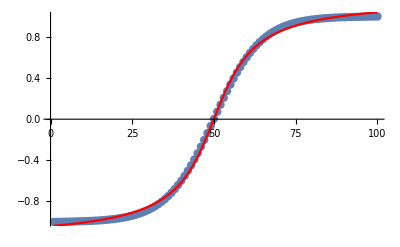

```mathematica
Show[
ListPlot[Table[Subscript[P, x],{x,1,100}]/.state,Mesh->All,Joined->True,PlotRange->All],
Plot[model/.param,{x,1,100},PlotStyle->Red]]
```

```mathematica
Energy=Sum[1040(Subscript[P, x+1]-Subscript[P, x])^2+5(Subscript[P, x]^2-1)^2,{x,0,100}]/.{Subscript[P, 0]->-1,Subscript[P, 101]->1};
```